```mathematica
dividedDiff[nodes_,vals_]:=(If[Length[nodes]==1,vals[[1]],((dividedDiff[nodes[[2;;Length[nodes]]],vals[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],vals[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]]))]);
 newtonPoly[nodes_, values_, x_] := (values[[1]]+Sum[dividedDiff[nodes[[1;;n]], values[[1;;n]]]*Product[x-nodes[[i]],{i,1,n-1}], {n, 2, Length[nodes]}]);
```

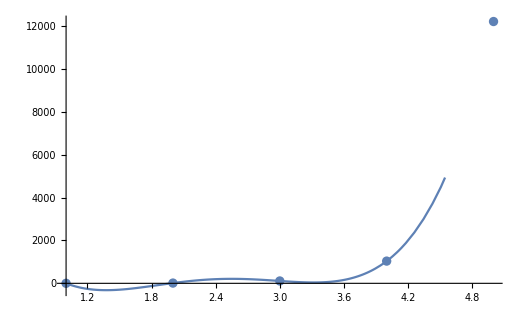
```mathematica
(*Using algibraic poly, the graph is not accurate because of the way polys behave*)

nodes = {1, 2,3,4 ,5};
values = {1,12,110,1037,12218};
pointPlot = ListPlot[Transpose[{nodes, values}]1];
p[x_]:=newtonPoly[nodes,values, x];
polyPlot = Plot[p[x], {x, 1 ,5 }];
Show[polyPlot, pointPlot, PlotRange->All]
-Graphics-
(*Notice how there is a dip before 2, this is not something that should be happening. A poly cant grow at too fast a rate and values like this arent interpolated very good with algebraic polys*)
(**)
```

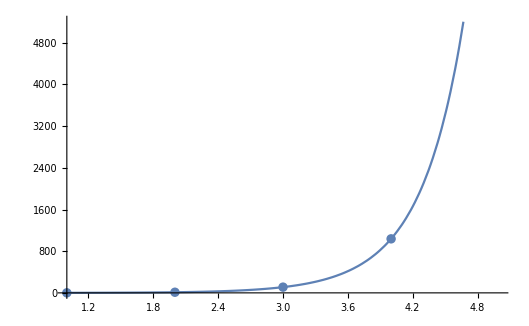
```mathematica
(*Using custom linear space, from the prev grapihc we can see that the function looks like an exponential one and thats why we make a linear space that is madee up of exponential functions*)
coefToFind = {a0, a1,a2,a3,a4};
q[x_]:= coefToFind[[1]]+coefToFind[[2]]*E^(x)+coefToFind[[3]]*E^(2x)+coefToFind[[4]]*E^(3x) + coefToFind[[5]]E^(4x);
nodes = {1, 2,3,4 ,5};

newCoefs =NSolve [{q[nodes[[1]]]==values[[1]],q[nodes[[2]]]==values[[2]],q[nodes[[3]]]==values[[3]],q[nodes[[4]]]==values[[4]],q[nodes[[5]]]==values[[5]]},coefToFind];
replacedPoly [x_]:= q[x]/.newCoefs[[1]];

replacedPoly[x]
0.10506027266812802-0.38237615607931047 ⅇ^x+0.25728020409206975 ⅇ^(2 x)+0.0016505219993470477 ⅇ^(3 x)+2.4982952195592255*^-6 ⅇ^(4 x)
replacedPolyPlot = Plot[replacedPoly[x], {x, 1, 5}];
Show[{replacedPolyPlot, pointPlot}]
-Graphics-
```